### O problema:

#### Parametros

```mathematica
xmin=0.0001;
xmax=2.5;
n=1;
β=0.5;
α=2;
```

#### Equacoes

```mathematica
eq3=x^2 h''[x]==x h'[x]-α^2 x^2(1-h[x])g[x]^2
eq1=x^2 f''[x]==-x f'[x]+β/4 x^2 f[x](f[x]^2+g[x]^2-2)
eq2=x^2 g''[x]==-x g'[x]+n^2 g[x](1-h[x])^2+β/4 x^2 g[x](f[x]^2+g[x]^2-2)
```

x^2 h''[x]==-4 x^2 g[x]^2 (1-h[x])+x h'[x]

x^2 f''[x]==0.125 x^2 f[x] (-2+f[x]^2+g[x]^2)-x f'[x]

x^2 g''[x]==0.125 x^2 g[x] (-2+f[x]^2+g[x]^2)+g[x] (1-h[x])^2-x g'[x]

### Cond. de contorno devidas:

```mathematica
eqbc1={eq1,f'[xmin]==0,f[xmax]==1};
eqbc2={eq2,g[xmin]==0,g[xmax]==1};
eqbc3={eq3,h[xmin]==0,h[xmax]==1};
eqs ={eqbc1,eqbc2,eqbc3};
sols=NDSolve[eqs,{f,g,h},{x,xmin,xmax}];

fsol=sols⟦1,1,2⟧;
gsol=sols⟦1,2,2⟧;
hsol=sols⟦1,3,2⟧;
```

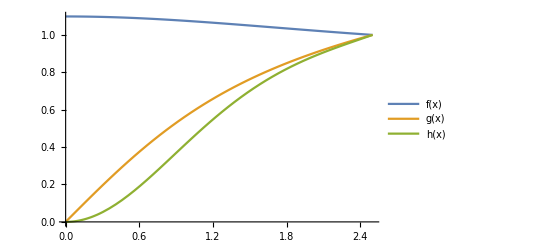

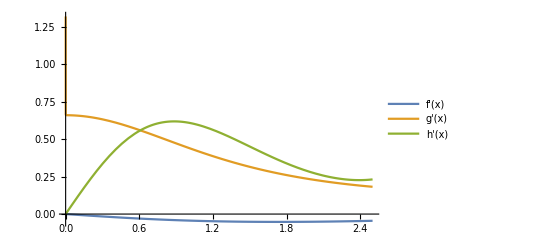

```mathematica
Plot[{fsol[x],gsol[x],hsol[x]},{x,xmin,xmax},PlotLegends->{"f(x)","g(x)","h(x)"}]
Plot[{fsol'[x],gsol'[x],hsol'[x]},{x,xmin,xmax},PlotLegends->{"f'(x)","g'(x)","h'(x)"}]
```

### Cond. de contorno induzidas (pela solução acima):

```mathematica
fsol[xmin]
gsol'[xmin]
hsol'[xmin]
```

1.09868

1.31902

0.000119189

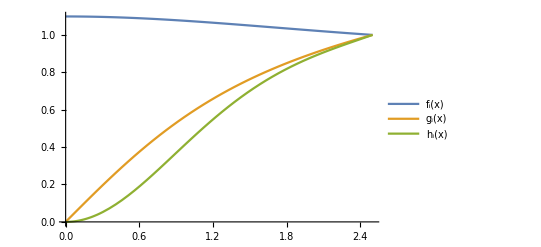

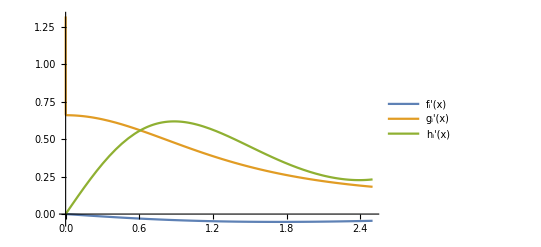

```mathematica
eqbci1={eq1,f'[xmin]==0,f[xmin]==1.09868};
eqbci2={eq2,g[xmin]==0,g'[xmin]==1.31902};
eqbci3={eq3,h[xmin]==0,h'[xmin]==0.000119189};
eqsi ={eqbci1,eqbci2,eqbci3};
solsi=NDSolve[eqsi,{f,g,h},{x,xmin,xmax}];

fsoli=solsi⟦1,1,2⟧;
gsoli=solsi⟦1,2,2⟧;
hsoli=solsi⟦1,3,2⟧;

Plot[{fsoli[x],gsoli[x],hsoli[x]},{x,xmin,xmax},PlotLegends->{"f_i(x)","g_i(x)","h_i(x)"}]
Plot[{fsoli'[x],gsoli'[x],hsoli'[x]},{x,xmin,xmax},PlotLegends->{"f_i'(x)","g_i'(x)","h_i'(x)"}]
```

### Casos assintóticos (funções de Bessel)

#### x→0

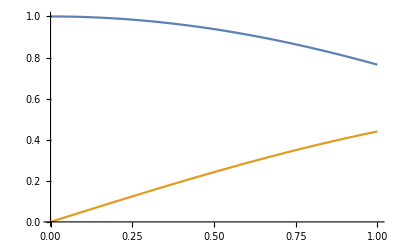

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x]},{x,0,1}]
```

#### x→∞

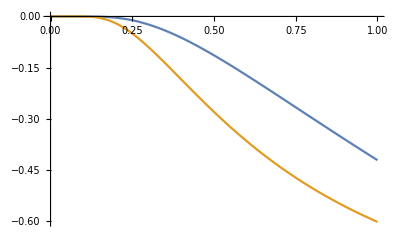

```mathematica
Plot[{-BesselK[0,1/x],-1/x BesselK[1,1/x]},{x,0,1}]
```